```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/software/Smoldyn/trunk/examples/S7_surfaces/surfacediffuse

```mathematica
timestep=10
diffconst=10
binlow=0
binhigh=100
binwidth=0.5
```

10

10

0

100

0.5

```mathematica
bendpos=30
```

30

```mathematica
(* Everything below here should take care of itself *)
```

```mathematica
(* Define functions *)
```

```mathematica
gauss[x_,mu_,sigma_]:=1/(sigma*Sqrt[2*Pi])*Exp[-(x-mu)^2/(2*sigma^2)]
```

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["simple2bout.txt"];
```

```mathematica
simdata
```

10 5431 5602 5942 6151 6430 7011 7033 7315 7584 7986 8028 8513 8635 9050 9641 9405 10090 10115 10887 10584 11083 11398 11995 11832 11808 12521 12914 12773 12833 13023 13347 13325 13573 13705 13998 13685 13782 14187 14010 14302 14178 14045 14185 13885 14068 13844 13596 13667 13393 13608 13081 12843 12780 12785 12310 11885 11930 11635 11277 11099 10717 10653 10165 10052 9622 9653 9158 8740 8649 8165 8083 7534 7308 6997 6759 6320 6167 5853 5637 5292 5013 4598 4681 4479 3813 3905 3656 3498 3367 2939 2920 2665 2369 2427 2209 1901 1952 1713 1734 1660 1208 1448 1227 1198 1014 968 709 984 718 738 498 724 494 459 520 246 489 233 229 233 227 242 233 237 253 0 256 0 229 0 0 265 0 0 0 261 233 0 0 0
10 0 0 0 226 276 0 0 0 233 0 0 225 0 236 0 262 225 264 237 226 226 258 258 456 243 508 517 471 746 465 699 765 1006 728 992 931 1201 1211 1468 1275 1764 1733 1760 1946 1953 2224 2538 2465 2634 2884 2926 3483 3282 3487 3940 3897 4284 4642 4711 5196

```mathematica
simdata2=StringReplace[simdata," "->","]
```

10,5431,5602,5942,6151,6430,7011,7033,7315,7584,7986,8028,8513,8635,9050,9641,9405,10090,10115,10887,10584,11083,11398,11995,11832,11808,12521,12914,12773,12833,13023,13347,13325,13573,13705,13998,13685,13782,14187,14010,14302,14178,14045,14185,13885,14068,13844,13596,13667,13393,13608,13081,12843,12780,12785,12310,11885,11930,11635,11277,11099,10717,10653,10165,10052,9622,9653,9158,8740,8649,8165,8083,7534,7308,6997,6759,6320,6167,5853,5637,5292,5013,4598,4681,4479,3813,3905,3656,3498,3367,2939,2920,2665,2369,2427,2209,1901,1952,1713,1734,1660,1208,1448,1227,1198,1014,968,709,984,718,738,498,724,494,459,520,246,489,233,229,233,227,242,233,237,253,0,256,0,229,0,0,265,0,0,0,261,233,0,0,0
10,0,0,0,226,276,0,0,0,233,0,0,225,0,236,0,262,225,264,237,226,226,258,258,456,243,508,517,471,746,465,699,765,1006,728,992,931,1201,1211,1468,1275,1764,1733,1760,1946,1953,2224,2538,2465,2634,2884,2926,3483,3282,3487,3940,3897,4284,4642,4711,5196

```mathematica
simdata3=ImportString[simdata2,"CSV"]
```

{{10,5431,5602,5942,6151,6430,7011,7033,7315,7584,7986,8028,8513,8635,9050,9641,9405,10090,10115,10887,10584,11083,11398,11995,11832,11808,12521,12914,12773,12833,13023,13347,13325,13573,13705,13998,13685,13782,14187,14010,14302,14178,14045,14185,13885,14068,13844,13596,13667,13393,13608,13081,12843,12780,12785,12310,11885,11930,11635,11277,11099,10717,10653,10165,10052,9622,9653,9158,8740,8649,8165,8083,7534,7308,6997,6759,6320,6167,5853,5637,5292,5013,4598,4681,4479,3813,3905,3656,3498,3367,2939,2920,2665,2369,2427,2209,1901,1952,1713,1734,1660,1208,1448,1227,1198,1014,968,709,984,718,738,498,724,494,459,520,246,489,233,229,233,227,242,233,237,253,0,256,0,229,0,0,265,0,0,0,261,233,0,0,0},{10,0,0,0,226,276,0,0,0,233,0,0,225,0,236,0,262,225,264,237,226,226,258,258,456,243,508,517,471,746,465,699,765,1006,728,992,931,1201,1211,1468,1275,1764,1733,1760,1946,1953,2224,2538,2465,2634,2884,2926,3483,3282,3487,3940,3897,4284,4642,4711,5196}}

```mathematica
simdata4=Join[Drop[simdata3[[2]],1],Drop[simdata3[[1]],1]]
```

{0,0,0,226,276,0,0,0,233,0,0,225,0,236,0,262,225,264,237,226,226,258,258,456,243,508,517,471,746,465,699,765,1006,728,992,931,1201,1211,1468,1275,1764,1733,1760,1946,1953,2224,2538,2465,2634,2884,2926,3483,3282,3487,3940,3897,4284,4642,4711,5196,5431,5602,5942,6151,6430,7011,7033,7315,7584,7986,8028,8513,8635,9050,9641,9405,10090,10115,10887,10584,11083,11398,11995,11832,11808,12521,12914,12773,12833,13023,13347,13325,13573,13705,13998,13685,13782,14187,14010,14302,14178,14045,14185,13885,14068,13844,13596,13667,13393,13608,13081,12843,12780,12785,12310,11885,11930,11635,11277,11099,10717,10653,10165,10052,9622,9653,9158,8740,8649,8165,8083,7534,7308,6997,6759,6320,6167,5853,5637,5292,5013,4598,4681,4479,3813,3905,3656,3498,3367,2939,2920,2665,2369,2427,2209,1901,1952,1713,1734,1660,1208,1448,1227,1198,1014,968,709,984,718,738,498,724,494,459,520,246,489,233,229,233,227,242,233,237,253,0,256,0,229,0,0,265,0,0,0,261,233,0,0,0}

```mathematica
Length[simdata4]
```

200

```mathematica
nmolec=Total[simdata4]
```

1000000

```mathematica
xvector=Table[i,{i,binlow+binwidth/2,binhigh-binwidth/2,binwidth}];
```

```mathematica
simdata5=Transpose[{xvector,simdata4}];
```

```mathematica
sigma=Sqrt[2*diffconst*timestep]
```

10 √2

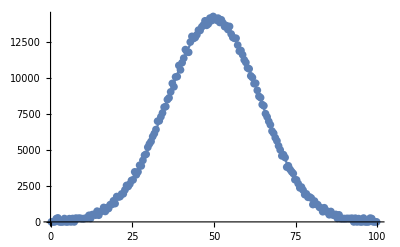

```mathematica
Show[{ListPlot[simdata5],Plot[nmolec*binwidth*gauss[x,50,sigma],{x,binlow,binhigh},PlotRange->All]},PlotRange->All]
```

```mathematica
residuals=Table[simdata4[[i]]-nmolec*binwidth*gauss[xvector[[i]],50,sigma],{i,1,Length[simdata4]}];
```

```mathematica
residuals2=Transpose[{xvector,residuals}];
```

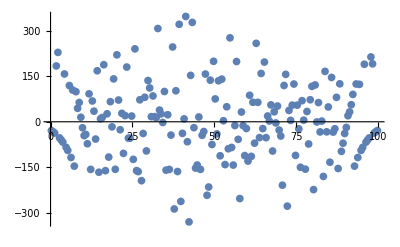

```mathematica
ListPlot[residuals2]
```